```mathematica
ClearAll["Global`*"]
```

#### ODEs

```mathematica
RodOde[nx0_?NumberQ,y0_?NumberQ,m0_?NumberQ]:=Block[
{Sol},
Sol=NDSolve[
{x'[s]==g*Cos[θ[s]],
y'[s]==g*Sin[θ[s]],
ny'[s]==k y[s],
θ'[s]==g*m[s],
m'[s]==g*(nx0*Sin[θ[s]]-ny[s]Cos[θ[s]]),
x[0]==0,y[0]==y0,θ[0]==0,ny[0]==0,m[0]==m0},
{x[s],y[s],θ[s],ny[s],m[s]},{s,0,L/2}][[1]];
{x[s]-L/2,y[s],θ[s]}/.Sol/.s->L/2
];

EquilSol[nx0_,y0_,m0_,g_]:=NDSolve[
{x'[s]==g*Cos[θ[s]],
y'[s]==g*Sin[θ[s]],
ny'[s]==k y[s],
θ'[s]==g*m[s],
m'[s]==g*(nx0*Sin[θ[s]]-ny[s]Cos[θ[s]]),
x[0]==0,y[0]==y0,θ[0]==0,ny[0]==0,m[0]==m0},
{x,y,θ,m,ny},{s,0,L/2}][[1]];

RodOdeContact[nx0_?NumberQ,y0_?NumberQ,m0_?NumberQ,g_,sc_?NumberQ,f_?NumberQ]:=Block[
{Sol1,Sol2,x1,y1,θ1,m1,ny1,Cond},
Sol1=NDSolve[
{x'[s]==g*Cos[θ[s]],
y'[s]==g*Sin[θ[s]],
ny'[s]==k y[s],
θ'[s]==g*m[s],
m'[s]==g*(nx0*Sin[θ[s]]-ny[s]Cos[θ[s]]),
x[0]==0,y[0]==y0,θ[0]==0,ny[0]==0,m[0]==m0},
{x[s],y[s],θ[s],ny[s],m[s]},{s,0,sc}][[1]];

x1=x[s]/.Sol1/.s->sc;
y1=y[s]/.Sol1/.s->sc;
θ1=θ[s]/.Sol1/.s->sc;
ny1=ny[s]/.Sol1/.s->sc;
m1=m[s]/.Sol1/.s->sc;

Cond={x1,θ1+π/2};

Sol2=NDSolve[
{x'[s]==g*Cos[θ[s]],
y'[s]==g*Sin[θ[s]],
ny'[s]==k y[s],
θ'[s]==g*m[s],
m'[s]==g*((nx0-f)*Sin[θ[s]]-ny[s]Cos[θ[s]]),
x[sc]==x1,y[sc]==y1,θ[sc]==θ1,ny[sc]==ny1,m[sc]==m1},
{x[s],y[s],θ[s],ny[s],m[s]},{s,sc,L/2}][[1]];


AppendTo[Cond,{x[s]-L/2,y[s],θ[s]}/.Sol2/.s->L/2];
Flatten[Cond]
];

EquilSolContactPlot[nx0_,y0_,m0_,g_,sc_,f_]:=Block[
{Sol1,Sol2,x1,y1,θ1,m1,ny1},
Sol1=NDSolve[
{x'[s]==g*Cos[θ[s]],
y'[s]==g*Sin[θ[s]],
ny'[s]==k y[s],
θ'[s]==g*m[s],
m'[s]==g*(nx0*Sin[θ[s]]-ny[s]Cos[θ[s]]),
x[0]==0,y[0]==y0,θ[0]==0,ny[0]==0,m[0]==m0},
{x[s],y[s],θ[s],ny[s],m[s]},{s,0,sc}][[1]];

x1=x[s]/.Sol1/.s->sc;
y1=y[s]/.Sol1/.s->sc;
θ1=θ[s]/.Sol1/.s->sc;
ny1=ny[s]/.Sol1/.s->sc;
m1=m[s]/.Sol1/.s->sc;

Sol2=NDSolve[
{x'[s]==g*Cos[θ[s]],
y'[s]==g*Sin[θ[s]],
ny'[s]==k y[s],
θ'[s]==g*m[s],
m'[s]==g*((nx0-f)*Sin[θ[s]]-ny[s]Cos[θ[s]]),
x[sc]==x1,y[sc]==y1,θ[sc]==θ1,ny[sc]==ny1,m[sc]==m1},
{x[s],y[s],θ[s],ny[s],m[s]},{s,sc,L/2}][[1]];

Show[ParametricPlot[{x[s],y[s]}/.Sol1,{s,0,sc}],ParametricPlot[{x[s],y[s]}/.Sol2,{s,sc,L/2}],PlotRange->All]

];
```

#### Initial solution

```mathematica
k=50;
L=1;
dγ=0.1;
g=1+dγ;
S=FindRoot[RodOde[a,b,c],{a,-35},{b,0.01},{c,-.4}]
```

{a→-35.5628,b→-0.00969776,c→-1.75148}

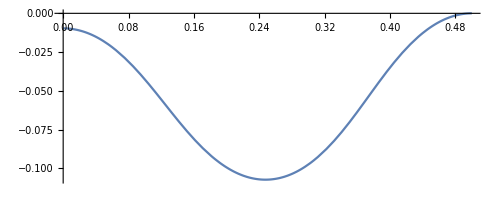

```mathematica
ParametricPlot[Evaluate[{x[s],y[s]}/.EquilSol[a/.S,b/.S,c/.S,g]],{s,0,L/2}]
```

#### Growth evolution to contact

```mathematica
Subscript[γ, 1]=1+dγ;
g=Subscript[γ, 1];
Subscript[S, 1]=FindRoot[RodOde[a,b,c],{a,-40},{b,0.01},{c,-.4}];
NN=30;
For[i=2,i≤NN,i++,
Subscript[γ, i]=Subscript[γ, i-1]+dγ;
g=Subscript[γ, i];
Subscript[S, i]=FindRoot[RodOde[a,b,c],{a,a/. Subscript[S, i-1]},{b,b/. Subscript[S, i-1]},{c,c/. Subscript[S, i-1]}];
];
```

```mathematica
Manipulate[
ParametricPlot[Evaluate[{x[s],y[s]}/.EquilSol[a/. Subscript[S, i],b/. Subscript[S, i],c/. Subscript[S, i],Subscript[γ, i]]],{s,0,L/2}],{i,1,NN,1}]
```

ReplaceAll::reps: {S_15} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ParametricPlot::plln: Limiting value L/2 in {s, 0, L/2} is not a machine-sized real number.

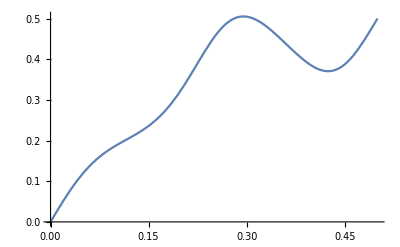

```mathematica
i=17;
Plot[Evaluate[x[s]/.EquilSol[a/. Subscript[S, i],b/. Subscript[S, i],c/. Subscript[S, i],Subscript[γ, i]]],{s,0,L/2}]
```

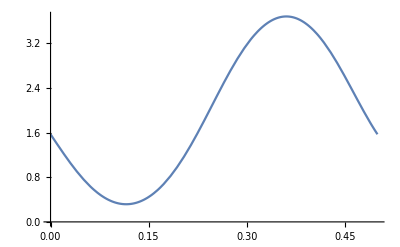

```mathematica
Plot[Evaluate[(θ[s]+π/2)/.EquilSol[a/. Subscript[S, i],b/. Subscript[S, i],c/. Subscript[S, i],Subscript[γ, i]]],{s,0,L/2}]
```

#### Contact solution

```mathematica
i=17;
g=Subscript[γ, i]+.01;
Sol=FindRoot[RodOdeContact[a,b,c,g,sc,f],{a,a/. Subscript[S, i]},{b,b/. Subscript[S, i]},{c,c/. Subscript[S, i]},{sc,.3075},{f,0.0}]
```

$Aborted

```mathematica
Norm[RodOdeContact[a/.Sol,b/.Sol,c/.Sol,g,sc/.Sol,f/.Sol]]
```

1.72602×10^-14

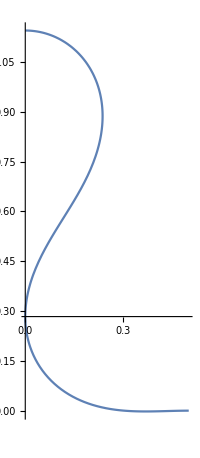

```mathematica
EquilSolContactPlot[a/.Sol,b/.Sol,c/.Sol,g,sc/.Sol,f/.Sol]
```

#### Continue the growth, solution with 1 CP

```mathematica
Sol
```

{a→-7.02769,b→1.14438,c→-4.44196,sc→0.307097,f→0.069853}

```mathematica
g
```

3.41

```mathematica
Subscript[Γ, 1]=g;
Subscript[SS, 1]=Sol;
NN=20;Subscript[Γ, 1]=g;
Subscript[SS, 1]=Sol;
NN=20;
i=2;
Subscript[Γ, i]=Subscript[Γ, i-1]+dγ;
Subscript[SS, i]=FindRoot[RodOdeContact[a,b,c,Subscript[Γ, i],sc,f],{a,a/. Subscript[SS, i-1]},{b,b/. Subscript[SS, i-1]},{c,c/. Subscript[SS, i-1]},{sc,sc/. Subscript[SS, i-1]},{f,f/. Subscript[SS, i-1]}];
For[i==3,i≤NN,i++,
Subscript[Γ, i]=Subscript[Γ, i-1]+dγ;
Subscript[SS, i]=FindRoot[RodOdeContact[a,b,c,Subscript[Γ, i],sc,f],{a,a/. Subscript[SS, i-1]},{b,b/. Subscript[SS, i-1]},{c,c/. Subscript[SS, i-1]},{sc,sc/. Subscript[SS, i-1]},{f,f/. Subscript[SS, i-1]}];
];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
Manipulate[EquilSolContactPlot[a/. Subscript[SS, i],b/. Subscript[SS, i],c/. Subscript[SS, i],Subscript[Γ, i],sc/. Subscript[SS, i],f/. Subscript[SS, i]],{i,1,NN,1}]
```

```mathematica
Manipulate[Norm[RodOdeContact[a/. Subscript[SS, i],b/. Subscript[SS, i],c/. Subscript[SS, i],Subscript[Γ, i],sc/. Subscript[SS, i],f/. Subscript[SS, i]]],{i,1,NN,1}]
```